# 16-Cell

### Author

Eric W. Weisstein
June 12, 2019

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Polytopes/16-Cell.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/16-Cell.html.

©2019 Wolfram Research, Inc. except for portions noted otherwise

## Construction

### As +/-1 tuples

```mathematica
pm[n_]:=Flatten[Outer[List,Sequence@@Table[{-1,1},{n}]],n-1]
```

```mathematica
Cell16Construction:=Module[
{vs={Permutations[{#1,0,0,0}]&@@@pm[1]}},
Union[Flatten[#,1]]&/@vs/Sqrt[2]
]
```

```mathematica
v=Join@@Cell16Construction
```

{{-1/(√2),0,0,0},{0,-1/(√2),0,0},{0,0,-1/(√2),0},{0,0,0,-1/(√2)},{0,0,0,1/(√2)},{0,0,1/(√2),0},{0,1/(√2),0,0},{1/(√2),0,0,0}}

```mathematica
e=Select[Subsets[Range[8],{2}],N[EuclideanDistance@@v[[#]],20]==1&]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{2,3},{2,4},{2,5},{2,6},{2,8},{3,4},{3,5},{3,7},{3,8},{4,6},{4,7},{4,8},{5,6},{5,7},{5,8},{6,7},{6,8},{7,8}}

### As a cross polytope

```mathematica
(* section 13.4 of Coxeter's Regular Polytopes *)
CrossPolytopeCoordinates[n_Integer?Positive]:=Module[{a,r,k},a=Table[Flatten[Table[Through[{Cos,Sin}[(2 r-1) Pi k/n]],{r,Floor[n/2]}]],{k,2 n}];
If[OddQ[n],Table[Join[a[[k]],{(-1)^k/Sqrt[2]}],{k,2 n}],(*Else*)a]/Sqrt[n]]
```

```mathematica
v=CrossPolytopeCoordinates[4]
```

{{1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2)},{0,1/2,0,-1/2},{-1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2)},{-1/2,0,-1/2,0},{-1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2)},{0,-1/2,0,1/2},{1/(2 √2),-1/(2 √2),-1/(2 √2),-1/(2 √2)},{1/2,0,1/2,0}}

```mathematica
e=Select[Subsets[Range[8],{2}],N[EuclideanDistance@@v[[#]],20]==1&]
```

{{1,2},{1,3},{1,4},{1,6},{1,7},{1,8},{2,3},{2,4},{2,5},{2,7},{2,8},{3,4},{3,5},{3,6},{3,8},{4,5},{4,6},{4,7},{5,6},{5,7},{5,8},{6,7},{6,8},{7,8}}

```mathematica
Length[e]
```

24

```mathematica
RecognizeGraph@System`Graph[Range[8],UndirectedEdge@@@e]
```

SixteenCellGraph

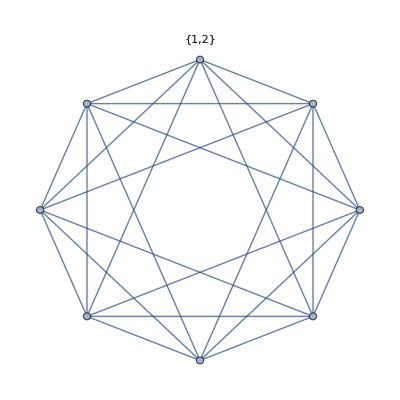
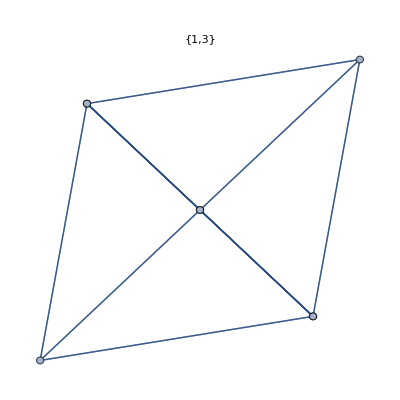
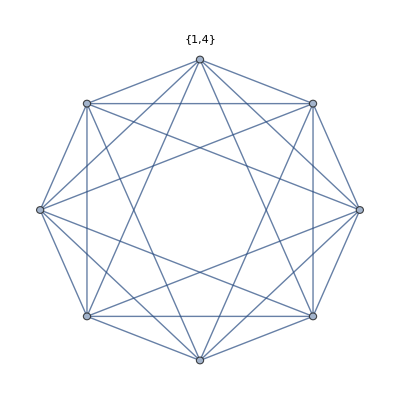
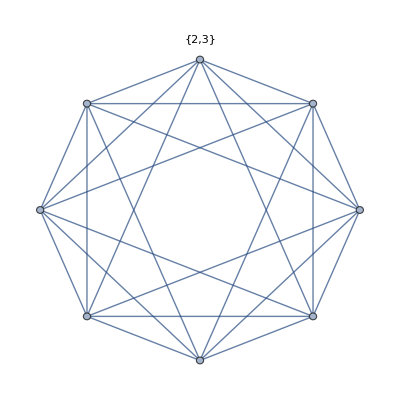
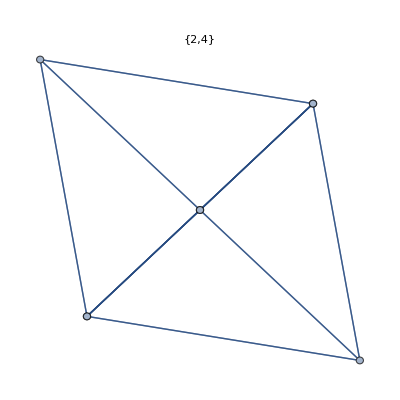
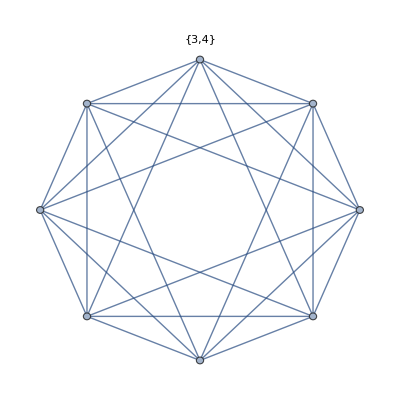

```mathematica
Show[System`Graph[Range[8],UndirectedEdge@@@e,VertexCoordinates->v[[All,#]]],PlotLabel->#]&/@Subsets[Range[4],{2}]
```

### VertexCount

```mathematica
Length/@Cell16Construction
```

{8}

```mathematica
Length[v]
```

8

### Circumradius

```mathematica
Max[FullSimplify[Norm/@v]]
```

1/(√2)

### Content

```mathematica
ConvexHullMesh[v]
```

```mathematica
RegionMeasure[%]
```

#### Wikipedia inequality

https://en.wikipedia.org/wiki/Cross-polytope

{x∈ℝ^n:x1≤1}

```mathematica
Integrate[Boole[Norm[{x,y},1]≤1],{x,y}∈FullRegion[2]]//Timing
```

{0.011918,2}

```mathematica
1/(√2)^3 Integrate[Boole[Norm[{x,y,z},1]≤1],{x,y,z}∈FullRegion[3]]//Timing
```

{2.42349,(√2)/3}

```mathematica
Norm[{x,y,z,w},1]
```

Abs[w]+Abs[x]+Abs[y]+Abs[z]

```mathematica
1/(√2)^4 Integrate[Boole[Norm[{x,y,z,w},1]≤1],{x,y,z,w}∈FullRegion[4]]//Timing
```

{24.4322,1/6}

#### Octahedron/line segment

```mathematica
{1,RegionMeasure[Octahedron[]]}
```

{1,(√2)/3}

#### Wikipedia formula

https://en.wikipedia.org/wiki/Cross-polytope #Higher _dimensions

The volume of the n-dimensional cross-polytope is 2^n/n!

```mathematica
Table[2^n/(2^(n/2)n!),{n,4}]
```

{√2,1,(√2)/3,1/6}

### Edges

```mathematica
EuclideanDistance@@@Subsets[Range[Length[v]],{2}]//Union
```

{1,2,3,4,5,6,7}

```mathematica
Length[e=Select[Subsets[Range[Length[v]],{2}],EuclideanDistance@@v[[#]]==√2&]]
```

24

```mathematica
Length[e=Select[Subsets[Range[Length[v]],{2}],N[EuclideanDistance@@v[[#]],20]==√2&]]
```

24

```mathematica
e
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{2,3},{2,4},{2,5},{2,6},{2,8},{3,4},{3,5},{3,7},{3,8},{4,6},{4,7},{4,8},{5,6},{5,7},{5,8},{6,7},{6,8},{7,8}}

### Faces

```mathematica
faces=Sort[FindCycle[Graph[Range[8],UndirectedEdge@@@e],{3},All][[All,All,1]]]
```

{{1,3,2},{1,3,7},{1,4,2},{1,4,3},{1,4,7},{1,5,2},{1,5,3},{1,5,6},{1,5,7},{1,6,2},{1,6,4},{1,6,7},{2,3,5},{2,3,8},{2,4,3},{2,4,6},{2,4,8},{2,5,8},{2,6,5},{2,6,8},{3,4,7},{3,4,8},{3,5,7},{3,5,8},{3,8,7},{4,7,6},{4,8,6},{4,8,7},{5,6,7},{5,8,6},{5,8,7},{6,7,8}}

```mathematica
Length[%]
```

32

### Cells

```mathematica
Select[Subsets[faces,{4}],Tally[Flatten[#]][[All,2]]==={3,3,3,3}&]/.Thread[faces->Range[Length[faces]]]
```

{{1,3,4,15},{1,6,7,13},{2,4,5,21},{2,7,9,23},{3,10,11,16},{5,11,12,26},{6,8,10,19},{8,9,12,29},{13,14,18,24},{14,15,17,22},{16,17,20,27},{18,19,20,30},{21,22,25,28},{23,24,25,31},{26,27,28,32},{29,30,31,32}}

```mathematica
Length[%]
```

16

### Distances

```mathematica
Union[N[Norm/@(Subtract@@@Subsets[Cell16,{2}])]]//Length
```

2

### Graph

```mathematica
RecognizeGraph[Graph[UndirectedEdge@@@e]]
```

SixteenCellGraph

### NetCount

```mathematica
2^5(2^7 3^3+1+3^2)
```

110912

## Graphics

Projection and animation from Russell Towle

### Figure

```mathematica
line[l_List]:=Line[Join[l,{l[[1]]}]]
```

```mathematica
Show[Graphics[line[Orthoplex[2]]],AspectRatio->Automatic]
```

⁃Graphics⁃

```mathematica
First@Union[Map[N[mag[#]]&,v334]](*circumradius*)
```

1.

```mathematica
d=Union[ Map[N[mag[First@v334-#]]&, Rest@v334],
SameTest->(Chop[#1-#2]==0&)];
c=Table[
a=Drop[v334,i-1];
{First@a,#}& /@ Select[Rest@a, N[mag[First@a-#]]<N[d[[2]]]&],
{i,Length[v334]}];
v=Map[#[[ spc[[1]] ]]&, v334];
g=Map[#[[ spc[[1]] ]]&, Flatten[c,1], {-2} ];
Show[Graphics3D[{Line /@ Union[g],PointSize[.02],Point/@v} ],
Boxed->False,
ViewPoint->{0,0,2}];
```

```mathematica
gr=FromEdges[Orthoplex[4],c];
ShowGraph[gr]
```

⁃Graphics⁃

```mathematica
{v,e}={V[gr],M[gr]}
```

{8,24}

```mathematica
deg=2;
k=KSubsets[Range[v-1],deg];
Print[{Binomial[v-1,deg],Length[k]}];
Position[IsomorphicQ[CirculantGraph[v,#],gr]&/@k,True]//Flatten
```

{21,21}

{}

```mathematica
deg=3;
k=KSubsets[Range[v-1],deg];
Print[{Binomial[v-1,deg],Length[k]}];
Position[IsomorphicQ[CirculantGraph[v,#],gr]&/@k,True]//Flatten
```

{35,35}

{1,3,8,13,19,24,31,35}

### Animation

```mathematica
(* Animation *)
(* r= which 3-space:1(w=0),2(z=0),3(y=0),4(x=0)*)
(* t= PlotRange*)

PolytopeMovie[vertices_List,ang_List:{0,Pi,Pi/30},r_:1,t_:2,opts___]:=Module[{v,d,c,a,v1,g},
Table[v=(rota4[#1,i,i]&)/@vertices;
d=Union[(N[mag[v[[1]]-#1]]&)/@Rest[v],SameTest->(Chop[#1-#2]==0&)];
c=Table[a=Drop[v,i-1]; ({First[a],#1}&)/@Select[Rest[a],Chop[N[mag[First[a]-#1]]-d[[1]]]==0&],{i,Length[v]}];
v1=(#1[[spc[[r]]]]&)/@v;
g=Map[#1[[spc[[r]]]]&,Flatten[c,1],{-2}];
Show[Graphics3D[{Line/@Union[g],PointSize[0.02],Point/@v1}],Boxed->False,PlotRange->{{-t,t},{-t,t},{-t,t}},opts],{i,ang[[1]],ang[[2]]-ang[[3]],ang[[3]]}]
]
```

```mathematica
movie=PolytopeMovie[vi334,{0,Pi,Pi/15},1,2]
```

```mathematica
WriteLiveAnimationForm["crosspol.m",movie]
```